# μLang — Computationally Generating a Morphologically Average Conlang Lexicon from Multilingual Translations

Constructed languages, or conlangs, are languages that were artificially created instead of being naturally evolved over several generations. A crucial part of every conlang is the lexicon — the vocabulary. While most lexicons are generated manually or through the help of randomized selection, I present several methods to generating a quantitatively “average” lexicon, that is, generating new words that may have similar features, spelling, or pronunciation compared to several translations of the same word in different languages.

## Initial Setup

I start with a simple word and and using translations provided by the Wolfram Language. In this case, I’m using “language”.

```mathematica
KEYWORD = "language";
```

Get the top 35 most spoken languages

```mathematica
languages=EntityClass["Language",{"TotalSpeakers"->TakeLargest[35]}]//EntityList
```

{Chinese,English,Mandarin Chinese,Hindi,Arabic,Spanish,French,Standard Arabic,Bengali,Russian,Portuguese,Malay,Indonesian,Urdu,German,Japanese,Lahnda,Swahili,Swahili,Marathi,Telugu,Turkish,Yue Chinese,Tamil,Western Panjabi,Wu Chinese,Korean,Vietnamese,Hausa,Javanese,Egyptian Arabic,Italian,Persian,Gujarati,Thai}

Get raw translations of “sun” to the determined languages

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[KEYWORD, languages]];
rawTranslations//Short
```

{Chinese→語言,English→language,Mandarin Chinese→語言,Hindi→भाषा,Arabic→لُغَة,Spanish→lenguaje,French→langue,Standard Arabic→NotAvailable,Bengali→ভাষা,Russian→язык,Portuguese→língua,Malay→NotAvailable,Indonesian→bahasa,Urdu→زبان,German→Sprache,Japanese→詞,Lahnda→NotAvailable,Swahili→NotAvailable,Swahili→lugha,Marathi→भाषा,Telugu→ఛాష,Turkish→dil,Yue Chinese→语言,Tamil→மொழி,Western Panjabi→NotAvailable,Wu Chinese→NotAvailable,Korean→언어,Vietnamese→tiếng,Hausa→harshe,Javanese→basa,Egyptian Arabic→NotAvailable,Italian→lingua,Persian→NotAvailable,Gujarati→ભાષા,Thai→ภาษา}

Standardize all translated words — Transliterate to the Roman alphabet and ensure all words are lowercase

```mathematica
translatedList=DeleteCases[DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]], "notavailable"]
```

{language,bhasa,lughat,lenguaje,langue,azyk,lingua,bahasa,zban,sprache,ci,lugha,chasa,dil,moli,tieng,harshe,basa}

## Most Common Letter

Naturally, this is the very first idea I jumped to. I counted the most frequent letter at every index, found the average length of the original words, and concatenated the most common letters together.

Split each word into a List of characters

```mathematica
charLists = Characters /@ translatedList;
charLists//Short
```

{{l,a,n,g,u,a,g,e},{b,h,a,s,a},{l,u,g,h,a,t},{l,e,n,g,u,a,j,e},{l,a,n,g,u,e},{a,z,y,k},{l,i,n,g,u,a},{b,a,h,a,s,a},«3»,{l,u,g,h,a},{c,h,a,s,a},{d,i,l},{m,o,l,i},{t,i,e,n,g},{h,a,r,s,h,e},{b,a,s,a}}

Find the average length of all words

```mathematica
avgLen=Round[Mean[Length/@charLists]]
```

5

For words shorter in length than the average length, pad the List with dashes. For words longer than the average length, truncate the List accordingly.

```mathematica
augmentedLists=Map[Function[chars,If[Length[chars]>avgLen,Take[chars,avgLen],PadRight[chars,avgLen,"-"]]],charLists];
augmentedLists//Short
```

{{l,a,n,g,u},{b,h,a,s,a},{l,u,g,h,a},{l,e,n,g,u},{l,a,n,g,u},{a,z,y,k,-},{l,i,n,g,u},{b,a,h,a,s},{«1»},«1»,{c,i,-,-,-},{l,u,g,h,a},{c,h,a,s,a},{d,i,l,-,-},{m,o,l,i,-},{t,i,e,n,g},{h,a,r,s,h},{b,a,s,a,-}}

Transpose the charList for easier calculation of the most frequent character at every position

```mathematica
transposed=Transpose[augmentedLists];
```

Find the most frequency character at each position and generate the average word

```mathematica
mostFreqChar=Map[Function[col,Module[{counts,filtered},filtered=DeleteCases[col,"-"];If[filtered==={},"-",counts=Tally[filtered];
First@First@SortBy[counts,-Last[#]&]]]],transposed];
```

```mathematica
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]]
```

langa

While this method does “work,” it is rather boring. It always produces one very predictable word and isn’t very creative. To generate an exciting lexicon, I explored some other methods.

## Most Common Digram

My seconnd approach  was to split each word into digrams (pairs of consecutive letters) and find the most common digram in each position. Then, we can join the most common digrams together. For example, “su” is the first digram in “sun” and “un” is the second digram in “sun.” By using digrams, I hope to preserve more content in each word during any transition

Calculate the average syllable count

```mathematica
SYLLABLECOUNT = Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

Split each word into digrams and record the position of each digram.

```mathematica
positionedDigrams=Flatten[
Table[
If[
StringLength[word]>=pos+1,
{pos,StringTake[word,{pos,pos+1}]},
Nothing],
{word,translatedList},
{pos,StringLength[word]-1}
],1];
positionedDigrams//Short
```

{{1,la},{2,an},{3,ng},{4,gu},{5,ua},{6,ag},{7,ge},{1,bh},{2,ha},{3,as},{4,sa},{1,lu},{2,ug},{3,gh},{4,ha},{5,at},{1,le},{2,en},{3,ng},{4,gu},«37»,{3,as},{4,sa},{1,di},{2,il},{1,mo},{2,ol},{3,li},{1,ti},{2,ie},{3,en},{4,ng},{1,ha},{2,ar},{3,rs},{4,sh},{5,he},{1,ba},{2,as},{3,sa}}

Group digrams by their position

```mathematica
groupedByPosition=GroupBy[positionedDigrams,First->Last];
Iconize[groupedByPosition]
```

Count the frequency of each digram in each position

```mathematica
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
countsByPosition//First
```

<|la→2,bh→1,lu→2,le→1,az→1,li→1,ba→2,zb→1,sp→1,ci→1,ch→1,di→1,mo→1,ti→1,ha→1|>

Get the most frequent digram in each position

```mathematica
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}]
```

{{la},{an},{ng},{gu},{ua},{ag},{ge}}

Generate new words by combining the most frequent digrams

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables:=RandomInteger[{Max[1, SYLLABLECOUNT-2], Min[Length[topDigramsByPosition], SYLLABLECOUNT+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]]

mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{10}]]
```

{laanng,la,laannggu,laan}

This isn’t great either. While there are some pronounceable words, this method is very basic and relies on the most common digrams. In fact, both of the previous methods relied very strictly on the most frequent characters with extremely basic substitution algorithms.

## Genetic Evolution

A different approach is to imagine the original list of translated words as a base “population.” Through a genetic algorithm, we can “evolve” the population and generate new words that are similar but completely unique. A genetic algorithm has a few parts:

Population: This is a set of possible solutions. In this case, the population is a List of possible “average” words. We will generate the starting population by randomly combining digrams from the original word list. Then, we will evolve the population.

Fitness: This a function that evaluates how “good” any individual is. Our fitness metric will measure how similar an individual is to the starting word list.

Selection: We want to select the top n most fit individuals to continue into the next population

Recombination: We can combine two “parents”, or parts of two words from a generation to form a “child” for the succeeding generation. We use one-point and two-point crossover.

One point crossover:

Takes the minimum length of both parents

For each character position, randomly select a character from either parent

Produces offspring with length equal to the shorter parent

Two point crossover:

Selects two random crossover points within the string length

Takes the beginning from parent 1, middle section from parent 2, and end from parent 1

Maintains the length of the shorter parent

Length-varying two point crossover:

Performs two-point crossover like the previous function

The resulting offspring can have different lengths than the parents

Enforces a maximum length constraint (MAXLENGTH) by truncating if necessary

At the end, I went with length-varying two point crossover as it gave me the most flexibility and creativity in terms of word generation.

Mutation: Each generation, we randomly alter some words to simulate random genetic mutation. This introduces more variability in the population and allows the population to explore a greater breadth of possibilities. We will randomly replace a letter or digram in some  randomly chosen words.

Define important variables. populationSize is the size of the population each generation and mutationRate

```mathematica
Clear[populationSize, generations, mutationRate, topDigramsByPosition, fitnessFunction, population, randomString, allBest];
populationSize=100;
generations=500;
mutationRate=0.08;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}]
allBest = {};
words = translatedList;
charSet = Flatten[topDigramsByPosition];
MAXLENGTH = Round[Mean[StringLength/@ words]]
```

{{la,lu,ba,bh,le},{an,ha,ug,en,zy},{ng,as,gh,yk,ha},{gu,sa,ha,as,ac},{ua,at,ue,sa,ch},{ag,aj,he},{ge,je}}

5

Our fitness function will calculate the average Levenshtein distance between a candidate word and each word in the original word list

```mathematica
fitnessFunction[candidate_String]:=Module[{maxDistance},
  maxDistance=Max[EditDistance[candidate,#] & /@ words];
  1-N[Mean[EditDistance[candidate,#] & /@ words]/maxDistance]
]
```

The fitness of a word similar to possible KEYWORD translations is significantly greater than a completely unrelated fitness word

```mathematica
fitnessFunction[WordTranslation[KEYWORD, "Spanish"][[1]]]
```

0.270833

```mathematica
fitnessFunction["random word"]
```

0.0707071

Here is our list of possible digrams

```mathematica
charSet
```

{la,lu,ba,bh,le,an,ha,ug,en,zy,ng,as,gh,yk,ha,gu,sa,ha,as,ac,ua,at,ue,sa,ch,ag,aj,he,ge,je}

Create our original population by randomly combining digrams

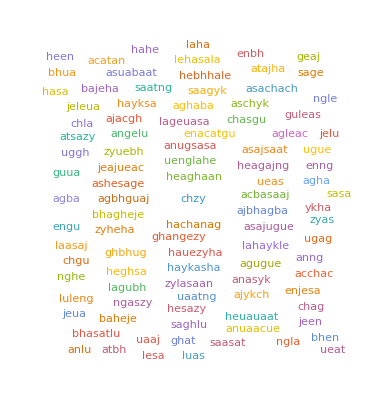

```mathematica
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT,SYLLABLECOUNT+2}]];
population=Table[randomString[],{populationSize}];
WordCloud[%]
```

With everything set up, I can simulate several hundred generations of evolution. I implemented one-point, two-point, and length-varied two-point crossover.

Implementation of crossover algorithms

```mathematica
onePointCrossover[p1_,p2_]:=Module[{len,chars1,chars2},len=Min[StringLength[p1],StringLength[p2]];
chars1=Characters[p1];
chars2=Characters[p2];
StringJoin@Table[RandomChoice[{chars1[[i]],chars2[[i]]}],{i,1,len}]];

twoPointCrossover[p1_,p2_]:=Module[{len,pt1,pt2,c1,c2},len=Min[StringLength[p1],StringLength[p2]];
{pt1,pt2}=Sort@RandomSample[Range[len],2];
c1=Characters[p1];
c2=Characters[p2];
StringJoin@Join[Take[c1,pt1-2],Take[c2,{pt1,pt2}],Drop[c1,pt2]]];

lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[Length[child]>MAXLENGTH,child=Take[child,MAXLENGTH]];
StringJoin[child]];
```

Implementation of string mutation

```mathematica
mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];
```

I record the best/”most fit” word each generation

```mathematica
allBest=Table[fitnesses=fitnessFunction/@population;
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
population=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
bestCandidate,
{gen,1,generations}
];

bestWordGeneticPool=First@MaximalBy[allBest,fitnessFunction];
Print["Best word found: ",bestWordGeneticPool];
Print["Fitness: ",fitnessFunction[bestWordGeneticPool]];
```

Best word found: ahhs

Fitness: 0.4375

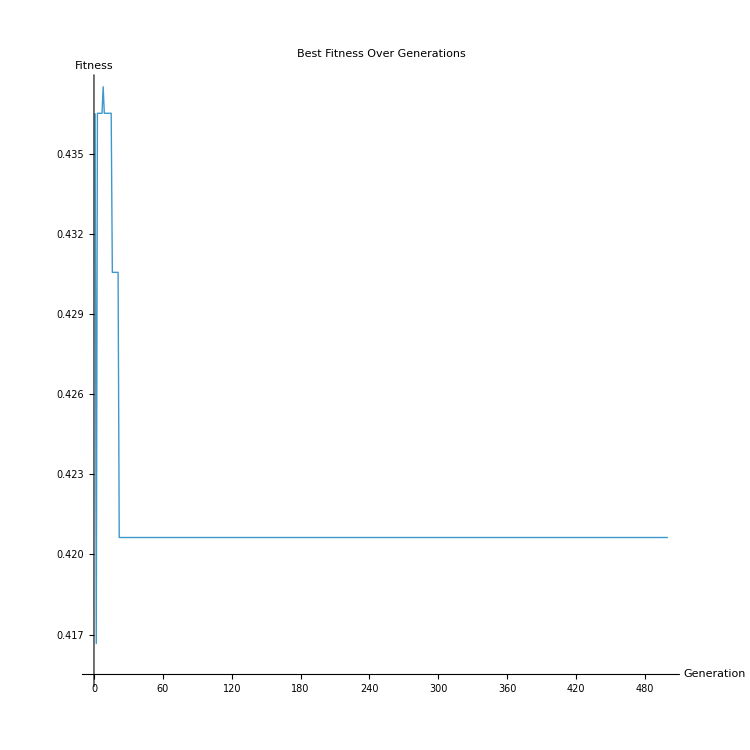

```mathematica
fitnessOverTime=Table[fitnessFunction[allBest[[i]]],{i,1,Length[allBest]}];
ListLinePlot[fitnessOverTime,PlotLabel->"Best Fitness Over Generations",AxesLabel->{"Generation","Fitness"},PlotStyle->Thick, ImageSize->{750, 750}, AspectRatio->1]
```

## String Optimization

Linguistic evolution can also be viewed as an optimization problem. I want to continuously evolve a string to be have the lowest average edit distance to all the multilingual words. I take a string and evolve it through several hundred generations. Each generation, I find the word that is farthest away (in Levenshtein Distance) to the evolving string. Then, I change one character in the evolving string to match a character in the most distant word. The choice of which character to use as a replacement is determined by a weighted probability. More common characters in that position are more likely to be used as the substitute. Over hundreds of generations, the evolving string takes on features of all the multilingual words.

Set up basic variables

```mathematica
Clear[baseWord, testList, padChar, baseWordStates, targetWords,GENERATIONS];
baseWord=StringJoin@RandomChoice[CharacterRange["a", "z"], 5];
startingWord = baseWord;
testList=translatedList;
padChar="_";
baseWordStates={baseWord};
targetWords={};
GENERATIONS=400;
```

First, calculate the probability weights for each character

```mathematica
calculateCharFrequencies[wordList_]:=Module[{maxLen,paddedWords,freqTables},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
freqTables=Table[Counts[StringTake[#,{pos}]&/@paddedWords],{pos,1,maxLen}];
freqTables];

normalizeFrequencies[freqTable_]:=Module[{nonZeroEntries,total},
nonZeroEntries=Select[freqTable,#>0&];
total=Total[Values[nonZeroEntries]];
If[total==0,freqTable,Association[#->If[freqTable[#]>0,N[freqTable[#]/total],0]&/@Keys[freqTable]]]];

getAllChars[wordList_]:=Module[{maxLen,paddedWords,allChars},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
allChars=Union[Flatten[Characters/@paddedWords]];
allChars];

allPossibleChars=getAllChars[testList];
rawFrequencies=calculateCharFrequencies[testList];

charFreqWeights=Table[Module[{posFreq,normalizedFreq},posFreq=rawFrequencies[[i]];
Do[If[!KeyExistsQ[posFreq,char],posFreq[char]=0],{char,allPossibleChars}];
normalizeFrequencies[posFreq]],{i,1,Length[rawFrequencies]}];

pad[w1_,w2_]:=Module[{maxLen,p1,p2},maxLen=Max[StringLength[w1],StringLength[w2]];
{StringPadRight[w1,maxLen,padChar],StringPadRight[w2,maxLen,padChar]}];

wordDifference[w1_,w2_]:=EditDistance[Pad[w1, w2][[1]], Pad[w1, w2][[2]]];

mostDifferentWord[base_,list_]:=Module[{diffs},diffs=Table[{word,wordDifference[base,word]},{word,list}];
First@MaximalBy[diffs,Last]];

findDifferingIndices[str1_,str2_]:=Module[{minLen,diffs},minLen=Min[StringLength[str1],StringLength[str2]];
diffs=Select[Range[minLen],StringTake[str1,{#}]=!=StringTake[str2,{#}]&];
diffs]

evolveToward[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i},
{basePadded, targetPadded} = pad[base, target];
diffIndices=findDifferingIndices[basePadded, targetPadded];
If[
diffIndices==={},
basePadded,
i=RandomChoice[diffIndices];
basePadded=StringReplacePart[basePadded,Part[Characters[targetPadded], i],{i,i}];basePadded
]
];

weightedRandomTarget[base_,list_]:=Module[{diffs,total,weights},
diffs=Table[{word,wordDifference[base,word]},{word,list}];
total=Total[diffs[[All,2]]];
If[total==0,

RandomChoice[list],
weights=(diffs[[All,2]]^3)/Total[diffs[[All,2]]^3];
RandomChoice[weights->diffs[[All,1]]]]
];

randomMutation[word_,rate_:0.05]:=Module[{chars,mutated},chars=Characters[word];
mutated=Map[If[RandomReal[]<rate,RandomChoice[CharacterRange["a","z"]~Join~{padChar}],#]&,chars];
StringJoin[mutated]];

layoutTestWords[baseWord_,testList_]:=Module[{angles,positions,dist,x,y},angles=Subdivide[0,2*Pi,Length[testList]][[1;;-2]];
positions={};
Do[dist=wordDifference[baseWord,testList[[i]]];
x=Cos[angles[[i]]]*dist;
y=Sin[angles[[i]]]*dist;
AppendTo[positions,{testList[[i]],x,y}],{i,1,Length[testList]}];
positions];

evolveTowardWeighted[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i,targetChar,baseChar,weight},{basePadded,targetPadded}=pad[base,target];
diffIndices=findDifferingIndices[basePadded,targetPadded];
If[diffIndices==={},basePadded,
i=RandomChoice[diffIndices];
targetChar=StringTake[targetPadded,{i,i}];
baseChar=StringTake[basePadded,{i,i}];
weight=
If[
i<=Length[charFreqWeights],
chars=Keys[charFreqWeights[[i]]];
weights = Values[charFreqWeights[[i]]];
choice = RandomChoice[weights->chars];
StringReplacePart[basePadded, choice, {i, i}], basePadded]]];

evolutionData={};
baseWordStates={baseWord};
targetWords={};

bestWord=baseWord;
bestDistance=Mean[wordDifference[baseWord,#]&/@testList];

Do[target=weightedRandomTarget[baseWord,testList];
AppendTo[targetWords,target];
baseWord=evolveTowardWeighted[baseWord,target];
(*baseWord=randomMutation[baseWord,0.1];*)
AppendTo[baseWordStates,baseWord];
currentDistance=Mean[wordDifference[baseWord,#]&/@testList];
If[currentDistance<bestDistance,bestDistance=currentDistance;
bestWord=baseWord;],{gen,1,GENERATIONS}];

bestWord=StringReplace[bestWord,"_"->""];
Print["Best word found: ",bestWord];
Print["Best average distance: ",N[bestDistance]];

testPositions=layoutTestWords[baseWordStates[[1]],testList];
positionDict=Association[#[[1]]->{#[[2]],#[[3]]}&/@testPositions];
```

Best word found: ladaha

Best average distance: 4.61111

```mathematica
createEvolutionAnimation[]:=Module[{frames,maxFrames,basePos={0,0},targetPos,newX,newY,t=0.25},maxFrames=Length[baseWordStates];
frames=Table[Module[{currentWord,target,bx,by,tx,ty},
currentWord=baseWordStates[[frame]];
If[frame<=Length[targetWords],target=targetWords[[frame]],target=targetWords[[-1]]];
targetPos=positionDict[target];
tx=targetPos[[1]];
ty=targetPos[[2]];
If[frame==1,{bx,by}={0,0},newX=basePos[[1]]+t*(tx-basePos[[1]]);
newY=basePos[[2]]+t*(ty-basePos[[2]]);
basePos={newX,newY};
{bx,by}=basePos;];
Show[Graphics[{Gray,Table[Text[Style[StringReplace[testPositions[[i,1]],"_"->""],FontSize->12],{testPositions[[i,2]],testPositions[[i,3]]}],{i,1,Length[testPositions]}],Red,Thickness[0.01],Line[{{bx,by},{tx,ty}}],Red,Text[Style[StringReplace[currentWord,"_"->""],FontSize->18,Bold],{bx,by}],Red,Text[Style["Target: "<>StringReplace[target,"_"->""],FontSize->12],{0,9.5}],Blue}],PlotRange->{{-10,10},{-10,10}},Axes->False,Frame->False,ImageSize->{400,400}]],{frame,1,maxFrames}];
ListAnimate[frames,AnimationRate->5,AnimationRepetitions->1]];

evolutionAnimation=createEvolutionAnimation[];
evolutionAnimation
```

```mathematica
plotEvolutionProgress[baseWordStates_,testList_]:=Module[{distances,generations},distances=Table[Mean[wordDifference[baseWordStates[[i]],#]&/@testList],{i,1,Length[baseWordStates]}];
generations=Range[0,Length[baseWordStates]-1];
ListLinePlot[MovingAverage[Transpose[{generations,distances}], 3],PlotLabel->"Evolution Progress: Average Distance to Multilingual Wordlist",AxesLabel->{"Generation","Average Distance"},PlotStyle->{Red,Thick},GridLines->Automatic, AspectRatio->1, ImageSize->{550, 550}]]
```

```mathematica
visualizeDistanceMatrix[wordList_]:=Module[{matrix,n},n=Length[wordList];
matrix=Table[wordDifference[wordList[[i]],wordList[[j]]],{i,n},{j,n}];
ArrayPlot[matrix,ColorFunction->"Rainbow",PlotLabel->"Word Distance Matrix",ImageSize->{1200, 1200},FrameLabel->{"Words","Words"},PlotLegends->Automatic,FrameTicks->{Table[{i,wordList[[i]]},{i,n}],Table[{i,wordList[[i]]},{i,n}]}]]
```

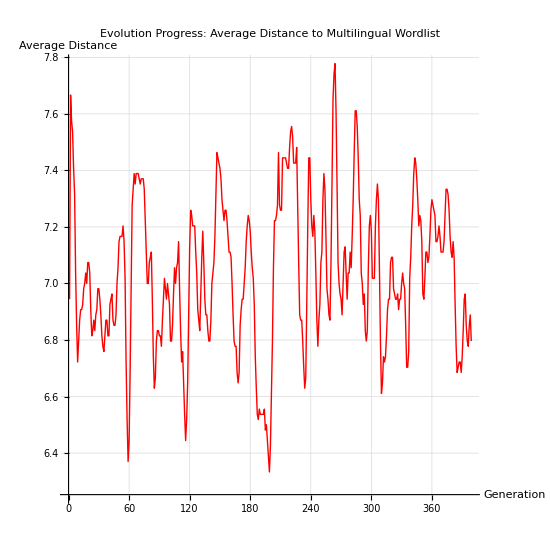

```mathematica
plotEvolutionProgress[baseWordStates, testList]
```

```mathematica
visualizeDistanceMatrix[testList]
```

-Graphics-

## Generation with Neural Net Features

A more modern approach may be to take advantage of neural net embeddings. A neural net/deep learning model encodes words in a numeric representation called embeddings or feature vectors. For text, embeddings usually encode semantic meaning. We can ask the neural net to generate new words with similar embedding values as the training set (the original word list), generating new but similar words.

```mathematica
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

```mathematica
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
```

```mathematica
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

```mathematica
results = 
 NetTrain[net, <|"Input" -> translatedList|>, All, LossFunction -> "Loss",   MaxTrainingRounds ->500]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:500  rounds:500  time:13s  examples/s:732
data | ,,  training examples:18  processed examples:9000  skipped examples:0
method | ,,  ADAMoptimizer  batch size18CPU
round | ,,  loss:4.99×10^-1  error:19.6%
 | 
 | ]

```mathematica
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}]
```

NetChain[<3>]

```mathematica
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
```

```mathematica
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList]
```

{baha,chas,hars,ling,lugh,spra}

```mathematica
allPossibleWords = Flatten[Join[{newAvgWords,bestWordGeneticPool, mostDigramGenerated, mostFreqCharWord, bestWord}]]
```

{baha,chas,hars,ling,lugh,spra,ahhs,laanng,la,laannggu,laan,langa,dbwyd}

```mathematica
extractor=NetChain[{trainednet,AggregationLayer[Max,1]}]
```

NetChain[<2>]

## Ease of pronunciation

Now that we have a list of possibly generated words from our different methods,

```mathematica
allPossibleWords
```

{baha,chas,hars,ling,lugh,spra,ahhs,laanng,la,laannggu,laan,langa,dbwyd}

## Evaluation and Visualization

```mathematica
allPossibleWords
```

{baha,chas,hars,ling,lugh,spra,ahhs,laanng,la,laannggu,laan,langa,dbwyd}

```mathematica
coordinatesAll=DimensionReduce[DeleteDuplicates[Join[allPossibleWords, translatedList]],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesAll;
```

```mathematica
coordinatesBase=DimensionReduce[DeleteDuplicates[translatedList],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesBase;
```

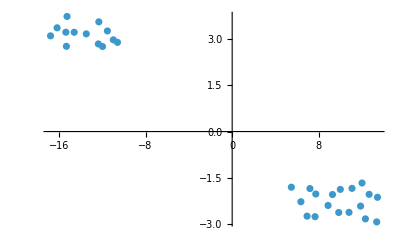

```mathematica
ListPlot[coordinatesAll]
```

```mathematica
coordinatesGen=DimensionReduce[DeleteDuplicates[allPossibleWords],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesGen;
```

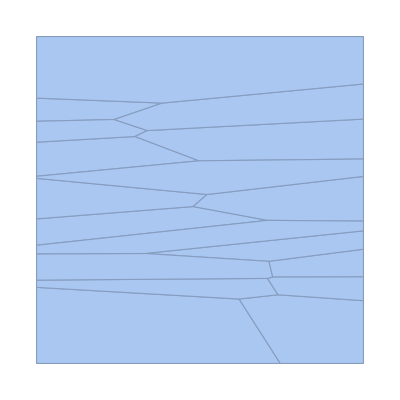

```mathematica
VoronoiMesh[coordinatesBase, AspectRatio->1]
```

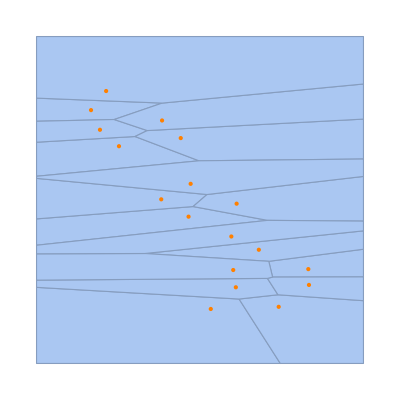

```mathematica
Show[%,Graphics[{Orange,Point[coordinatesBase]}, AspectRatio->1]]
```

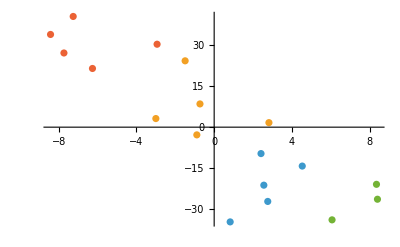

```mathematica
ListPlot[FindClusters[coordinatesBase,4,Method->"KMeans"]]
```

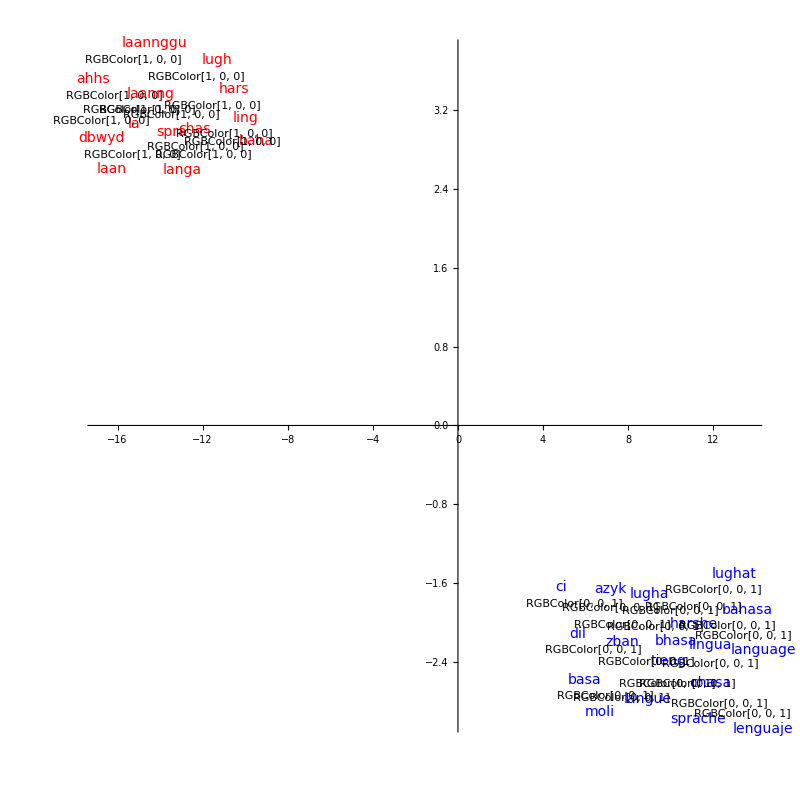

```mathematica
FeatureSpacePlot[
DeleteDuplicates[Join[
Labeled[#->Red, Style[#, Red, 14]]&/@allPossibleWords,
Labeled[#->Blue, Style[#, Blue, 14]]&/@translatedList
]],
FeatureExtractor->extractor,
LabelingSize->30,Axes->True, Method->"TSNE",ImageSize->{800,800}, AspectRatio->1
]
```

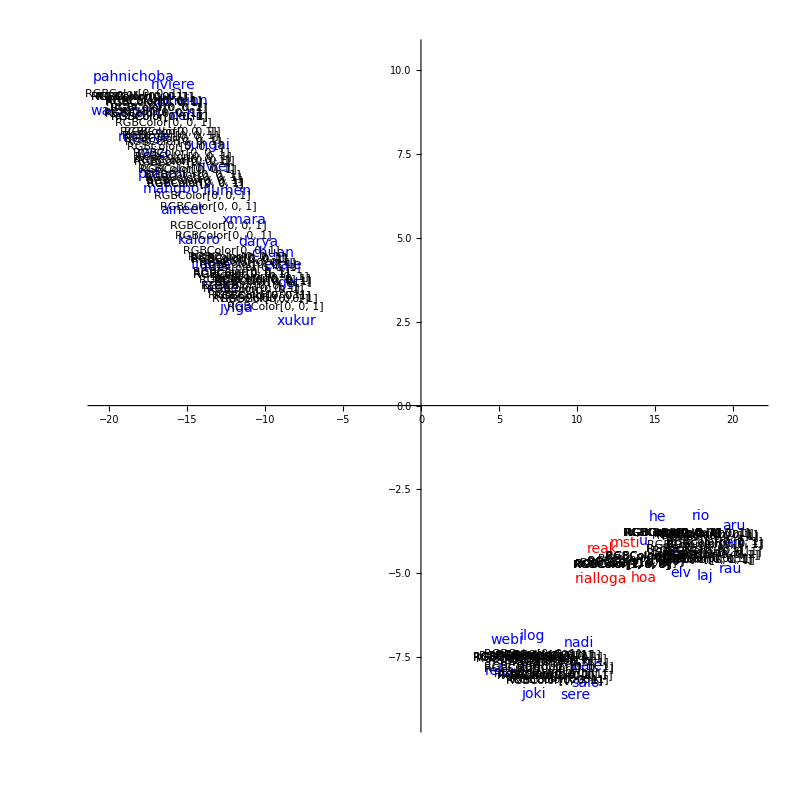

-Graphics-

## Metrics

We have some approaches which provide us with reasonable results. However, we need to quantify and visualize our newly generated words.

```mathematica
plotFitnessHeatmap[allPossibleWords_List]:=Module[{fitnessValues,reshapedValues,size,wordsMatrix},
	  fitnessValues=fitnessFunction /@ allPossibleWords;
	  size=Ceiling[Sqrt[Length[fitnessValues]]];
	  reshapedValues=PadRight[Partition[fitnessValues,size,size,{1,1},{}],{size,size},None];
	  wordsMatrix=PadRight[Partition[allPossibleWords,size,size,{1,1},""],{size,size},None];
	  ArrayPlot[reshapedValues,Color->"TemperatureMap",Frame->True,Mesh->True,MeshStyle->Gray,
	    PlotLabel->"Fitness Heatmap: Larger is better",ColorFunctionScaling->True,
	    Epilog->Flatten[
	      Table[
	        {
	          Text[Style[wordsMatrix[[i,j]],FontSize->12,Black],{j-0.5,size-i+0.25}],
	          Text[Style[NumberForm[reshapedValues[[i,j]],{4,2}],FontSize->12,Black],{j-0.5,size-i+0.75}]
	        },
	        {i,size},{j,size}
	      ]
	    ],
	    PlotLegends->BarLegend[{"TemperatureMap",{Min[fitnessValues],Max[fitnessValues]}}]
	  ]
	]
```

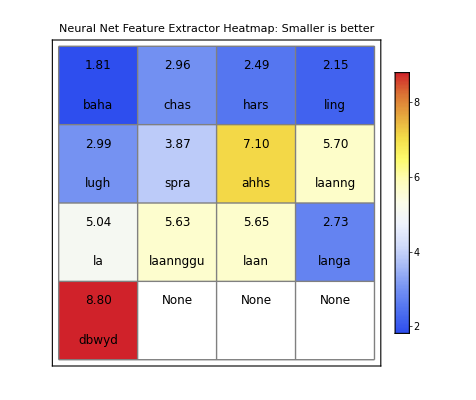

```mathematica
plotFitnessHeatmap[allPossibleWords]
```

```mathematica
WordCloud[StringTake[allPossibleWords, 1]]
```

-Graphics-

```mathematica
plotFitnessHeatmap[allPossibleWords_List]:=Module[{fitnessValues,reshapedValues,size,wordsMatrix},
	  fitnessValues=extractor /@ allPossibleWords;
	  size=Ceiling[Sqrt[Length[fitnessValues]]];
	  reshapedValues=PadRight[Partition[fitnessValues,size,size,{1,1},{}],{size,size},None];
	  wordsMatrix=PadRight[Partition[allPossibleWords,size,size,{1,1},""],{size,size},None];
	  ArrayPlot[reshapedValues,ColorFunction->"TemperatureMap",Frame->True,Mesh->True,MeshStyle->Gray,
	    PlotLabel->"Neural Net Feature Extractor Heatmap: Smaller is better",ColorFunctionScaling->True,
	    Epilog->Flatten[
	      Table[
	        {
	          Text[Style[wordsMatrix[[i,j]],FontSize->12,Black],{j-0.5,size-i+0.25}],
	          Text[Style[NumberForm[reshapedValues[[i,j]],{4,2}],FontSize->12,Black],{j-0.5,size-i+0.75}]
	        },
	        {i,size},{j,size}
	      ]
	    ],
	    PlotLegends->BarLegend[{"TemperatureMap",{Min[fitnessValues],Max[fitnessValues]}}]
	  ]
	]
```